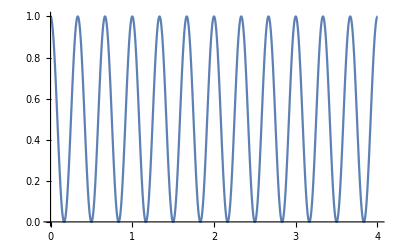

```mathematica
Plot[1/2*(1+{Sin[2*Pi*3*x+Pi/2]}),{x,0,4}]
```

```mathematica
f[x_,fr_]:=Exp[-2*Pi*I*fr*x];
g[t_] := 1/2*(1+Sin[2*Pi*3*t+Pi/2]);
Manipulate[ParametricPlot[{Re[g[t]*f[t,fr]],Im[g[t]*f[t,fr]]},{t,0,4}],{fr,0,3,0.01}]
```

```mathematica
ParametricPlot[{fr,Re[Integrate[(g[t]*f[t,fr]),{t,0,4}]]},{fr,0,5}, PlotRange->{{0,5},{-2,2}}]
```